# RRTV (2008)

## Figures (3,4,5)

## Conformal Block Definition

```mathematica
k[b_,z_]:=z^(b/2)Hypergeometric2F1[b/2,b/2,b,z];
G[l_,Δ_,z_,zbar_]:= (-1)^l/2^l(z zbar)1/(z-zbar)(-k[Δ-l-2,z]k[Δ+l,zbar]+k[Δ-l-2,zbar]k[Δ+l,z])
```

## Evaluation of F[z,zbar]

### Invariant Cross Ratios Definition

```mathematica
u[z_, zbar_]:= z zbar;
v[z_, zbar_]:=(1-z)(1-zbar)
```

### F[z,zbar] Definition

```mathematica
F[z_, zbar_]:=(v[z,zbar]^d G[l,Δ,z,zbar]-u[z,zbar]^d G[l,Δ,(1-z),(1-zbar)])/(u[z,zbar]^d-v[z,zbar]^d)
```

#### z=zbar Approximation

```mathematica
F2[z_]:=F[z,z+0.0001]
```

## Individual Plots for Different l,Δ; d=1

#### l=2, Δ=4,5.5,6

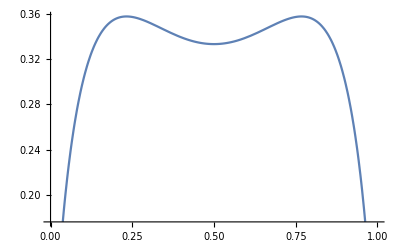

```mathematica
d=1; l=2; Δ=4;
Plot[F2[z], {z,0,1}]
```

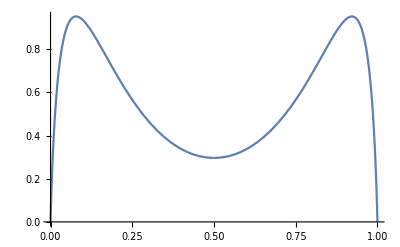

```mathematica
d=1; l=2; Δ=5.5;
Plot[F2[z], {z,0,1}]
```

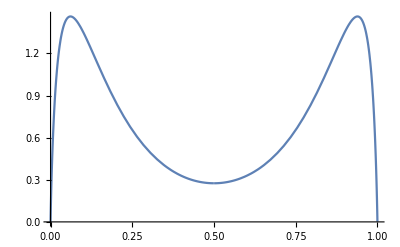

```mathematica
d=1; l=2; Δ=6;
Plot[F2[z], {z,0,1}]
```

#### l=4, Δ=6,6.5,7

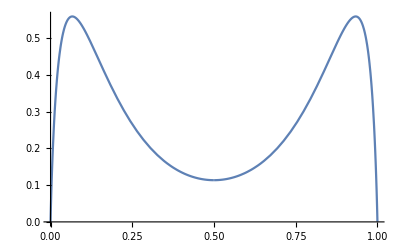

```mathematica
d=1; l=4; Δ=6;
Plot[F2[z], {z,0,1}]
```

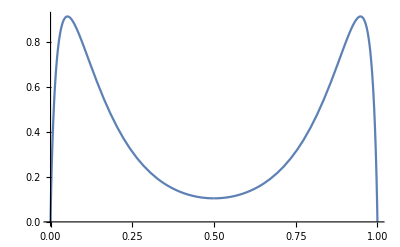

```mathematica
d=1; l=4; Δ=6.5;
Plot[F2[z], {z,0,1}]
```

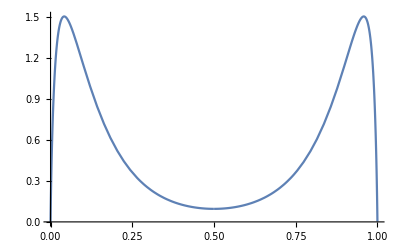

```mathematica
d=1; l=4; Δ=7;
Plot[F2[z], {z,0,1}]
```

#### l=0, Δ=2,3,4,5

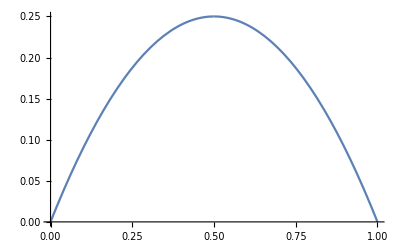

```mathematica
d=1; l=0; Δ=2;
Plot[F2[z], {z,0,1}]
```

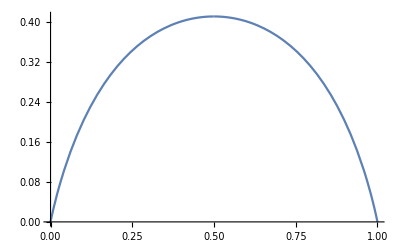

```mathematica
d=1; l=0; Δ=3;
Plot[F2[z], {z,0,1}]
```

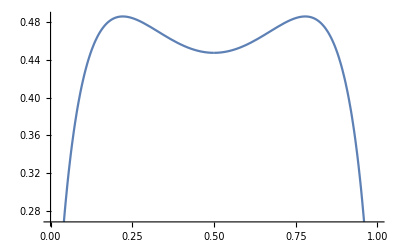

```mathematica
d=1; l=0; Δ=4;
Plot[F2[z], {z,0,1}]
```

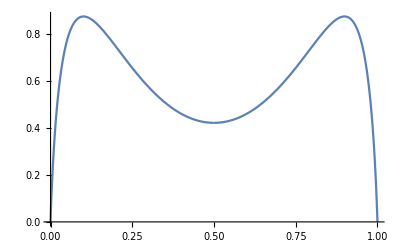

```mathematica
d=1; l=0; Δ=5;
Plot[F2[z], {z,0,1}]
```

#### A closer look at l=0 varying Δ

```mathematica
Ffull[l_,Δ_,z_,zbar_]:=(v[z,zbar]^d G[l,Δ,z,zbar]-u[z,zbar]^d G[l,Δ,(1-z),(1-zbar)])/(u[z,zbar]^d-v[z,zbar]^d)
```

```mathematica
F2ldelta[z_, l_, Δ_]:=Ffull[l,Δ,z,z+0.0001]
```

```mathematica
d=1; l=0;
Manipulate[Plot[F2ldelta[z,l,Δ],{z,0,1}],{Δ,2,5}]
```

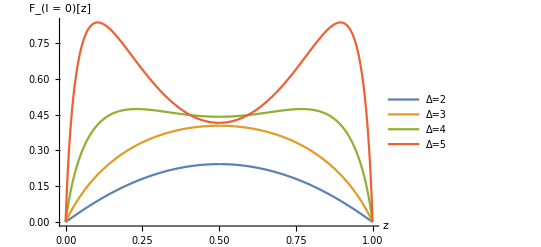

Fl0.jpg

```mathematica
PFl0=Plot[{F2ldelta[z, 0, 2],F2ldelta[z, 0, 3],F2ldelta[z, 0, 4],F2ldelta[z, 0, 5]},{z,0,1} ,AxesLabel->{"z","F_(l = 0)[z]"},PlotRange->All ,PlotLegends->{"Δ=2","Δ=3","Δ=4","Δ=5"}]
Export["Fl0.jpg",PFl0]
```

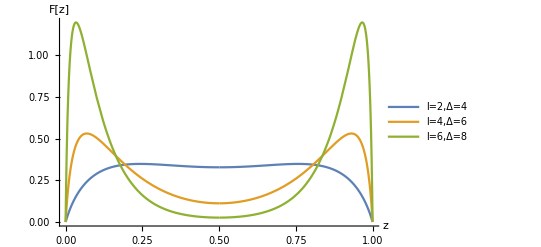

Fl2468.jpg

```mathematica
PFl2468=Plot[{F2ldelta[z, 2, 4],F2ldelta[z, 4, 6],F2ldelta[z, 6, 8]},{z,0,1} ,AxesLabel->{"z","F[z]"},PlotRange->All ,PlotLegends->{"l=2,Δ=4","l=4,Δ=6","l=6,Δ=8"}]
Export["Fl2468.jpg",PFl2468]
```

## Sum Rule

## Pre Factor p(l)

```mathematica
p[l_]:= 2^(l+1)(Factorial[l]^2/Factorial[2l])
```

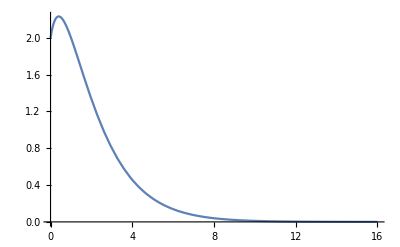

```mathematica
Plot[p[l],{l,0,16}]
```

## The sum rule for different values of l

```mathematica
d=1.01;
```

### l=0,2,4,8,16

```mathematica
S0[z_]:=p[0]F2ldelta[z, 0,2];
S2[z_]:=S0[z]+p[2]F2ldelta[z, 2,4];
S4[z_]:=S2[z]+p[4]F2ldelta[z,4,6];
S8[z_]:=S4[z]+p[8]F2ldelta[z,8,10];
S16[z_]:=S8[z]+p[16]F2ldelta[z,16,18];
```

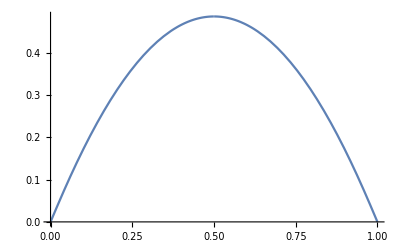

```mathematica
Plot[S0[z],{z,0,1}]
```

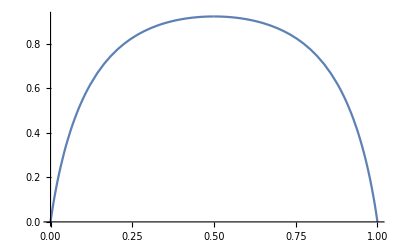

```mathematica
Plot[S2[z],{z,0,1}]
```

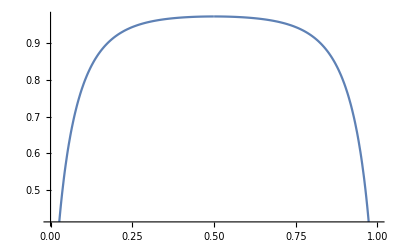

```mathematica
Plot[S4[z],{z,0,1}]
```

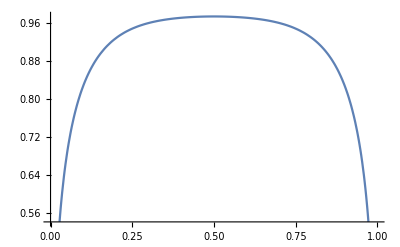

```mathematica
Plot[S8[z],{z,0,1}]
```

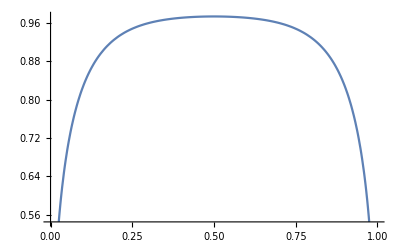

```mathematica
Plot[S16[z],{z,0,1}]
```

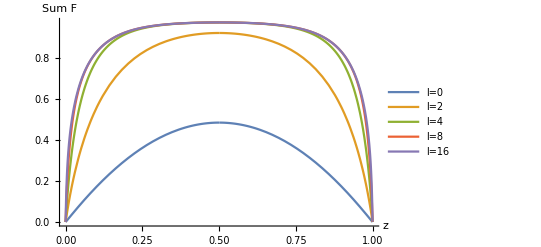

SumRule.jpg

```mathematica
Psumrule=Plot[{S0[z],S2[z],S4[z],S8[z],S16[z]},{z,0,1} ,AxesLabel->{"z","Sum F"},PlotRange->All ,PlotLegends->{"l=0","l=2","l=4","l=8","l=16"}]
Export["SumRule.jpg",Psumrule]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["SumRule.jpg"]]]
```